```mathematica
Quit[];
```

```mathematica
TwoLoopAmp1[s_,M_]:=-1/s(-Zeta[3]-2Zeta[2](Log[-x]-Log[1-x])+Log[-x]^2 Log[1+x]-2/3 Log[1-x]^3+(2Log[-x]-4Log[1-x])PolyLog[2,1+x]+4PolyLog[3,1+x]+2PolyLog[3,-x]+4PolyLog[3,1/(1-x)]+2PolyLog[3,x]-4PolyLog[3,(1+x)/(1-x)]+4PolyLog[3,(x+1)/(x-1)])/.{x->s/M^2};
```

```mathematica
TwoLoopAmp2[s_,M_]:=-2(-3/2-1/2(Lp+Lm)^2+Lp+Lm-x/2 Log[-x]+1/2(x-1/x)Log[1-x]+PolyLog[2,x])/.{x->s/M^2,Lp->EulerGamma+Log[-s/(4π)],Lm->EulerGamma+Log[M^2/(4π)]};
```

```mathematica
OneLoopAmp[s_]:=-EulerGamma+2+Log[(4π)/-s];
```

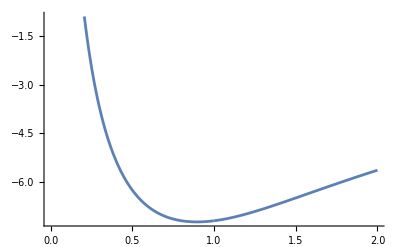

```mathematica
Plot[Re[TwoLoopAmp1[s,1]+TwoLoopAmp1[s,1]],{s,0,2}]
```

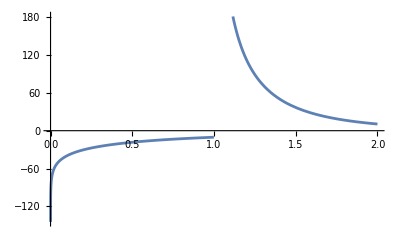

```mathematica
Plot[Im[TwoLoopAmp1[s,1]+TwoLoopAmp1[s,1]],{s,0,2}]
```

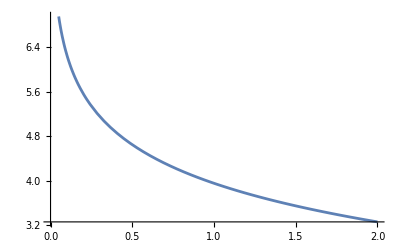

```mathematica
Plot[Re[OneLoopAmp[s]],{s,0,2}]
```

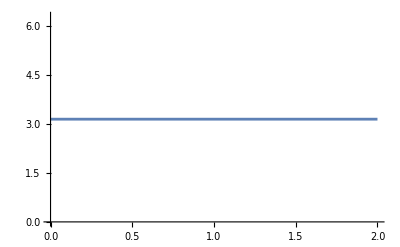

```mathematica
Plot[Im[OneLoopAmp[s]],{s,0,2}]
```